```mathematica
connectOneBarabasiAlbert[g_Graph/;ConnectedGraphQ[g]]:=g;
connectOneBarabasiAlbert[g_Graph]:=Module[{cmps=ConnectedComponents[g],pos},
pos=Flatten[Intersection[Position[VertexInDegree[seed],0],Select[cmps,Length[#]==Min[Length/@cmps]&]]];
If[pos=={},g,
EdgeAdd[g,RandomChoice[{1,2,3}]->RandomChoice[pos]]
]
]
```

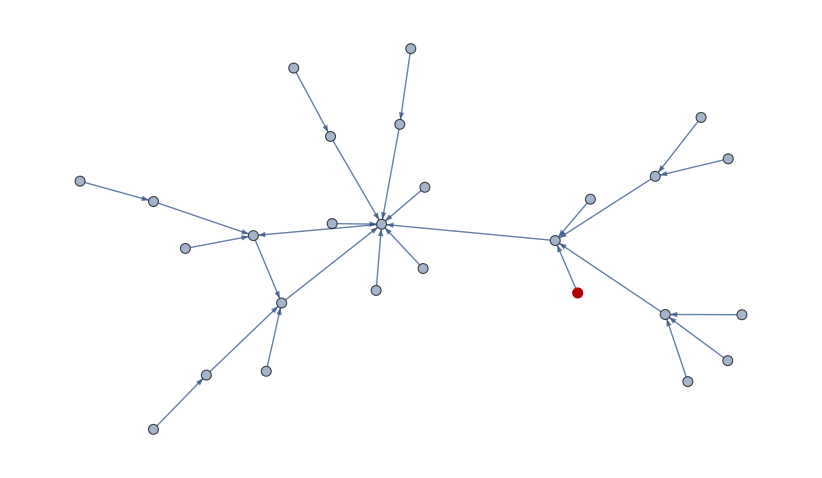

```mathematica
HighlightGraph[seed,27]
```

```mathematica
ConnectedComponents[seed]
```

{{1,2,3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Position[VertexInDegree[seed],0]
```

{{5},{10},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Length/@ConnectedComponents[seed]
```

{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Min[Length/@ConnectedComponents[seed]]
```

1

```mathematica
Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]
```

{{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Intersection[Position[VertexInDegree[seed],0],Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]]
```

{{5},{10},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

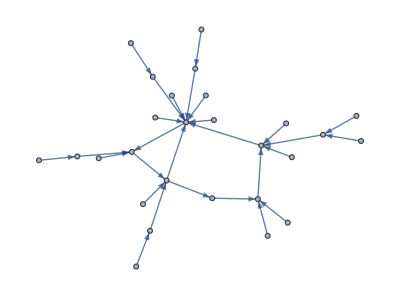

```mathematica
EdgeAdd[seed,RandomChoice[{1,2,3}]->RandomChoice[Flatten[Intersection[Position[VertexInDegree[seed],0],Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]]]]]
```

```mathematica
ConnectedComponents[%]
```

{{1,2,3,6,9,10},{4},{5},{7},{8},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

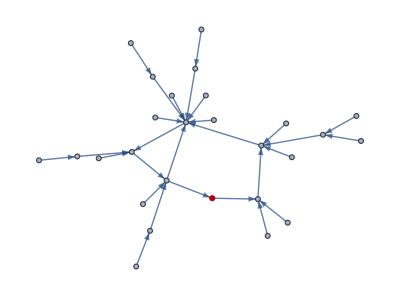

```mathematica
HighlightGraph[%%,10]
```

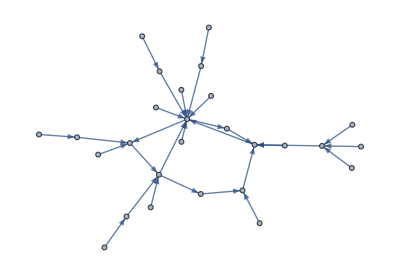

```mathematica
EdgeAdd[%%%,RandomChoice[{1,2,3}]->26]
```

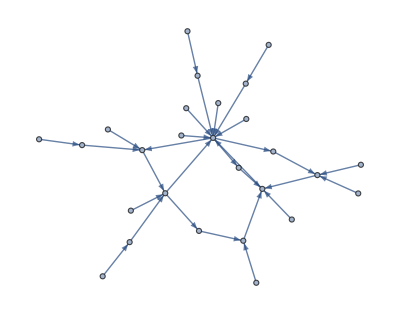

```mathematica
EdgeAdd[%,RandomChoice[{1,2,3}]->25]
```

```mathematica
ConnectedComponents[%]
```

{{1,2,3,6,9,16,25,26,27},{4},{5},{7},{8},{10},{11},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24}}

```mathematica
tst={{0,1,1,1,1},{0,0,1,1,0},{0,1,0,1,1},{1,1,0,0,0},{0,0,0,1,0}};
```

```mathematica
tst=AdjacencyGraph[tst]
```

-Graphics-

```mathematica
Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
graph=graphToNet[tst,Partition[Range[10],2]]
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
graph=graphToNet[tst,{4,3}]
```

{{{},{2,3,4,5}},{{},{3,4,5}},{{1,2,3,4},{2,4}},{{},{1,3}},{{},{4}}}

```mathematica
netEvolve[graph_List,T_Integer,top_Integer]:=Module[
{marbles=graph[[All,1]],n=Length[graph]},
NestList[add[graph,remove[graph,#],#,top]&,marbles,T]
]
```

```mathematica
mrb=
```

```mathematica
graph
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
netEvolve[graph,,5]
```

{{{1,2},{3,4},{5,6},{7,8},{9,10}},{{1,2},{3,4},{5},{7,8,6,10},{9}},{{1},{3,4,5},{10},{7,8,6,2},{9}},{{},{4,5,1},{10,3,6},{7,8,2,9},{}}}

```mathematica
fillWith[marbles_Integer]:=Module[{int=Floor[marbles/M],float=Mod[marbles,M],ret,count=1},
ret=RandomSample[ConstantArray[int,M]+Join[ConstantArray[1,float],ConstantArray[0,M-float]]];
Table[If[ret[[i]]==0,{},count=count+ret[[i]];Range[count-ret[[i]],count-1]],{i,M}]
]
```

```mathematica
ct=1
```

1

```mathematica
RandomSample[ConstantArray[Floor[(3M+2)/M],M]+Join[ConstantArray[1,Mod[3M+2,M]],ConstantArray[0,M-Mod[3M+2,M]]]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Table[If[%[[i]]==0,{},ct=ct+%[[i]];Range[ct-%[[i]],ct-1]],{i,Length[%]}]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12},{13,14,15},{16,17,18},{19,20,21},{22,23,24},{25,26,27},{28,29,30},{31,32,33},{34,35,36},{37,38,39},{40,41,42},{43,44,45},{46,47,48},{49,50,51,52},{53,54,55},{56,57,58},{59,60,61},{62,63,64},{65,66,67},{68,69,70},{71,72,73},{74,75,76},{77,78,79},{80,81,82},{83,84,85},{86,87,88},{89,90,91},{92,93,94},{95,96,97},{98,99,100},{101,102,103},{104,105,106},{107,108,109},{110,111,112},{113,114,115},{116,117,118},{119,120,121,122},{123,124,125},{126,127,128},{129,130,131},{132,133,134},{135,136,137},{138,139,140},{141,142,143},{144,145,146},{147,148,149},{150,151,152},{153,154,155},{156,157,158},{159,160,161},{162,163,164},{165,166,167},{168,169,170},{171,172,173},{174,175,176},{177,178,179},{180,181,182},{183,184,185},{186,187,188},{189,190,191},{192,193,194}}

```mathematica
Length/@%==%%
```

True

```mathematica
Range[1,1]
```

{1}